## Data

```mathematica
fa1[t_]=A*Exp[-I*(Δ-R)*t/2]+B*Exp[-I*(Δ+R)*t/2]
fa2[t_]=J*Exp[I*(Δ-R)*t/2]+K*Exp[I*(Δ+R)*t/2]
```

A ⅇ^(-1/2 ⅈ t (-R+Δ))+B ⅇ^(-1/2 ⅈ t (R+Δ))

ⅇ^(1/2 ⅈ t (-R+Δ)) J+ⅇ^(1/2 ⅈ t (R+Δ)) K

```mathematica
Da1[t_]=D[fa1[t],t]
Da2[t_]=D[fa2[t],t]
```

-1/2 ⅈ A ⅇ^(-1/2 ⅈ t (-R+Δ)) (-R+Δ)-1/2 ⅈ B ⅇ^(-1/2 ⅈ t (R+Δ)) (R+Δ)

1/2 ⅈ ⅇ^(1/2 ⅈ t (-R+Δ)) J (-R+Δ)+1/2 ⅈ ⅇ^(1/2 ⅈ t (R+Δ)) K (R+Δ)

```mathematica
da1[t_]=I*Ω/2*Exp[-I*Δ*t/2]*a20
da2[t_]=I*Ω/2*Exp[I*Δ*t/2]*a10
a10=1/Sqrt[2]
a20=Exp[I*ϕ]/Sqrt[2]
```

(ⅈ ⅇ^(-1/2 ⅈ t Δ+ⅈ ϕ) Ω)/(2 √2)

(ⅈ ⅇ^((ⅈ t Δ)/2) Ω)/(2 √2)

1/(√2)

ⅇ^(ⅈ ϕ)/(√2)

```mathematica
Da1[0]
Da2[0]
da1[0]
da2[0]
```

-1/2 ⅈ A (-R+Δ)-1/2 ⅈ B (R+Δ)

1/2 ⅈ J (-R+Δ)+1/2 ⅈ K (R+Δ)

(ⅈ ⅇ^(ⅈ ϕ) Ω)/(2 √2)

(ⅈ Ω)/(2 √2)

```mathematica
Solve[{Da1[0]==da1[0],fa1[0]==a10},{A,B}]
Solve[{Da2[0]==da2[0],fa2[0]==a20},{J,K}]
```

{{A→(R+Δ+ⅇ^(ⅈ ϕ) Ω)/(2 √2 R),B→(R-Δ-ⅇ^(ⅈ ϕ) Ω)/(2 √2 R)}}

{{J→(ⅇ^(ⅈ ϕ) R+ⅇ^(ⅈ ϕ) Δ-Ω)/(2 √2 R),K→(ⅇ^(ⅈ ϕ) R-ⅇ^(ⅈ ϕ) Δ+Ω)/(2 √2 R)}}

## Solution for a1, a2

```mathematica
A1S=Simplify[((R+Δ+ⅇ^(ⅈ ϕ) Ω)/(2 √2 R))*Exp[-I*(Δ-R)*t/2]+((R-Δ-ⅇ^(ⅈ ϕ) Ω)/(2 √2 R))*Exp[-I*(Δ+R)*t/2]]
```

(ⅇ^(-1/2 ⅈ t (R+Δ)) ((1+ⅇ^(ⅈ R t)) R+(-1+ⅇ^(ⅈ R t)) (Δ+ⅇ^(ⅈ ϕ) Ω)))/(2 √2 R)

```mathematica
A2S=Simplify[((ⅇ^(ⅈ ϕ) R+ⅇ^(ⅈ ϕ) Δ-Ω)/(2 √2 R))*Exp[I*(Δ-R)*t/2]+((ⅇ^(ⅈ ϕ) R-ⅇ^(ⅈ ϕ) Δ+Ω)/(2 √2 R))*Exp[I*(Δ+R)*t/2]]
```

(ⅇ^(-1/2 ⅈ t (R-Δ)) (ⅇ^(ⅈ (R t+ϕ)) (R-Δ)+ⅇ^(ⅈ ϕ) (R+Δ)-Ω+ⅇ^(ⅈ R t) Ω))/(2 √2 R)

## Populations

```mathematica
Pop1[ϕ_]=Simplify[Refine[A1S*Conjugate[A1S],{Element[t,Reals],Element[ϕ,Reals],Element[R,Reals],Element[Δ,Reals],Element[Ω,Reals]}]]
```

(((1+ⅇ^(ⅈ R t)) R+(-1+ⅇ^(ⅈ R t)) (Δ+ⅇ^(ⅈ ϕ) Ω)) Conjugate[(1+ⅇ^(ⅈ R t)) R+(-1+ⅇ^(ⅈ R t)) (Δ+ⅇ^(ⅈ ϕ) Ω)])/(8 R^2)

```mathematica
Pop2[ϕ_]=Simplify[Refine[A2S*Conjugate[A2S],{Element[t,Reals],Element[ϕ,Reals],Element[R,Reals],Element[Δ,Reals],Element[Ω,Reals]}]]
```

((ⅇ^(ⅈ (R t+ϕ)) (R-Δ)+ⅇ^(ⅈ ϕ) (R+Δ)-Ω+ⅇ^(ⅈ R t) Ω) (-Ω+Conjugate[ⅇ^(ⅈ (R t+ϕ)) (R-Δ)+ⅇ^(ⅈ ϕ) (R+Δ)+ⅇ^(ⅈ R t) Ω]))/(8 R^2)

```mathematica
Simplify[Pop1[0]]
Simplify[Pop2[0]]
```

(((1+ⅇ^(ⅈ R t)) R+(-1+ⅇ^(ⅈ R t)) (Δ+Ω)) Conjugate[(1+ⅇ^(ⅈ R t)) R+(-1+ⅇ^(ⅈ R t)) (Δ+Ω)])/(8 R^2)

((R+ⅇ^(ⅈ R t) (R-Δ)+Δ-Ω+ⅇ^(ⅈ R t) Ω) (-Ω+Conjugate[R+ⅇ^(ⅈ R t) (R-Δ)+Δ+ⅇ^(ⅈ R t) Ω]))/(8 R^2)

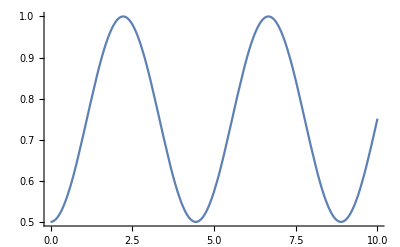

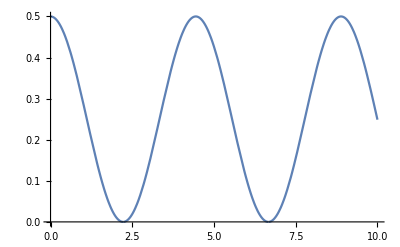

```mathematica
Plot[Simplify[Pop1[0]],{t,0,10},PlotRange->All]
Plot[Simplify[Pop2[0]],{t,0,10},PlotRange->All]
Δ:=1
Ω:=1
R:=Sqrt[Ω^2+Δ^2]
```

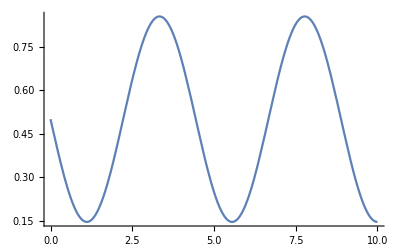

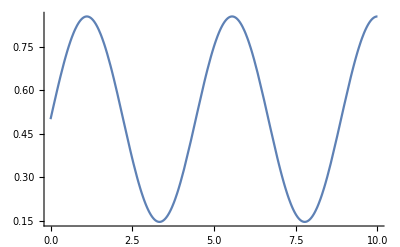

```mathematica
Plot[Simplify[Pop1[Pi/2]],{t,0,10},PlotRange->All]
Plot[Simplify[Pop2[Pi/2]],{t,0,10},PlotRange->All]
Δ:=1
Ω:=1
R:=Sqrt[Ω^2+Δ^2]
```